```mathematica
2+3
```

5

```mathematica
3*4
```

12

```mathematica
3/4
```

3/4

```mathematica
5/8
```

5/8

```mathematica
%*2
```

5/4

```mathematica
Pi
```

π

```mathematica
E
```

ⅇ

```mathematica
N[5*E]
```

13.5914

```mathematica
N[Log[3]]
```

1.09861

```mathematica
Log[3]
```

Log[3]

```mathematica
FractionalPart[Log[3]]
```

-1+Log[3]

```mathematica
N[Log[3],10]
```

1.098612289

```mathematica
IntegerPart[Log[3]]
```

1

```mathematica
Log[E]
```

1

```mathematica
f[x_]=(x^2+1)/(x-4)
```

(1+x^2)/(-4+x)

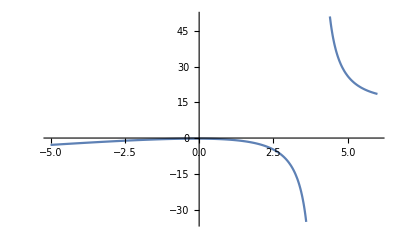

```mathematica
Plot[f[x], {x, -5,6}]
```

```mathematica
Limit[f[x],x->3]
```

-10

```mathematica
D[f[x], x]
```

(2 x)/(-4+x)-(1+x^2)/(-4+x)^2

```mathematica
f'[x]
```

(2 x)/(-4+x)-(1+x^2)/(-4+x)^2

```mathematica
f''[x]
```

2/(-4+x)-(4 x)/(-4+x)^2+(2 (1+x^2))/(-4+x)^3

```mathematica
Integrate[f[x],x]
```

1/2 (-48+8 x+x^2+34 Log[-4+x])

```mathematica
Integrate [f[x], {x, 2, 3}]
```

13/2-Log[131072]

```mathematica
∫_2^3 f[x]ⅆx
```

13/2-Log[131072]

```mathematica
Expand[(x+5)^5*(x-7)^11]
```

-6179146071875+3530940612500 x+302652052500 x^2-573597699500 x^3+76260081800 x^4+30408501732 x^5-8701790636 x^6-228719260 x^7+338551290 x^8-32156740 x^9-4247012 x^10+1025916 x^11-41920 x^12-7220 x^13+1020 x^14-52 x^15+x^16

```mathematica
Factor[%]
```

(-7+x)^11 (5+x)^5

```mathematica
Sum[n^2,{n,1,100}]
```

338350

```mathematica
∑_(n=1)^100 n^2
```

338350

```mathematica
Sum[n^2,{n,1,100,2}]
```

166650

```mathematica
N[∑_(n=1)^10 1/n^2, 20]
```

1.5497677311665406904

```mathematica
N[∑_(n=1)^100 1/n^2, 20]
```

1.6349839001848928651

```mathematica
N[∑_(n=1)^1000 1/n^2, 20]
```

1.6439345666815598031

```mathematica
N[∑_(n=1)^10000 1/n^2, 20]
```

1.6448340718480597698

```mathematica
∑_(n=1)^∞ 1/n^2
```

π^2/6

```mathematica
N[%]
```

1.64493

```mathematica
Solve[x^2-5x+6==0,x]
```

{{x→2},{x→3}}

```mathematica
NSolve[x^2–5x+6==0,x]
```

```mathematica
NSolve[x^7-5x+6==0,x]
```

{{x→-1.4462},{x→-0.798131-1.17329 ⅈ},{x→-0.798131+1.17329 ⅈ},{x→0.483132-1.23264 ⅈ},{x→0.483132+1.23264 ⅈ},{x→1.0381-0.312766 ⅈ},{x→1.0381+0.312766 ⅈ}}